```mathematica
Print["SaveFigures: ",SetterBar[Dynamic[SaveFigures],{True->"On",False->"Off"}]]
```

SaveFigures:  |

## Initialization

### Packages, Paths, common options

```mathematica
SetOptions[$FrontEnd,CommonDefaultFormatTypes->{"Output"->StandardForm}];
If[FileExistsQ["~/home-mpi/algebra/packages"],BaseDir="~/home-mpi",BaseDir="~"];
SetDirectory[BaseDir<>"/papers/sterile-nu/sim"];
$Path=Append[$Path,BaseDir<>"/algebra/packages"];
<<KPTools.m;

(* Taken from http://forums.wolfram.com/mathgroup/archive/1999/Apr/msg00028.html (slightly modified) *)
JHEPPlot[grObj_Graphics]:=Module[{fulopts,tcklst,th=0.004},
fulopts=FullOptions[grObj];
tcklst=FrameTicks/.fulopts/.{loc_,lab_,len:{_,_},{sty:___}}:>{loc,lab,2*len,{Directive[sty,Thickness[th]]}};
grObj/.Graphics[prims_,(opts__)?OptionQ]:>Graphics[prims,FrameTicks->tcklst,FrameTicksStyle->Thickness[th],FrameStyle->Thickness[th],opts]
];
```

### Reading GLoBES event rate files

```mathematica
glbSignalTot[Data_List]:=Transpose[{Data⟦1,1,All,1⟧,Plus@@Data⟦1,All,All,2⟧}];
glbBGTot[Data_List]:=Transpose[{Data⟦2,1,All,1⟧,Plus@@Data⟦2,All,All,2⟧}];
glbSignalBGTot[Data_List]:=Transpose[{Data⟦1,1,All,1⟧,(Plus@@Data⟦1,All,All,2⟧)+(Plus@@Data⟦2,All,All,2⟧)}];
```

## MiniBooNE

### Beam fluxes

```mathematica
DataFiles={
"0-code/glb/mb-2010/MBanti-flux.dat"
};
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Import[DataFiles⟦i⟧,"Table"];
];
```

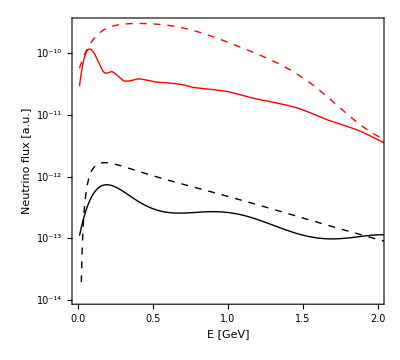

```mathematica
For[i=1,i≤Length[DataFiles],i++,
MyPlot[i]=ListLogPlot[Table[{#⟦1⟧,#⟦j⟧}&/@Data[i],{j,2,7}],Joined->True,PlotRange->{{0,2},All},
PlotStyle->{Directive[Black,Thick],Directive[Red,Thick],Directive[Blue,Thick],
Directive[Black,Dashed],Directive[Red,Dashed],Directive[Blue,Dashed]},FrameLabel->{"E [GeV]", "Neutrino flux [a.u.]"}];
];
Grid[{{MyPlot[1]}}]
```

### Preparation of AEDL file using data from MiniBooNE homepage

```mathematica
MCEventsAll=Import["0-code/glb/miniboone/data/miniboone_nunubarfullosc_ntuple.txt","Table"];
MCEventsNuBar=Import["0-code/glb/miniboone/data/miniboone_numubarnuebarfullosc_ntuple.txt","Table"];

BinBoundaries=Flatten[Import["0-code/glb/miniboone/data/miniboone_binboundaries_nubar_lowe.txt","Table"]];
BinWidths=Table[BinBoundaries⟦i+1⟧-BinBoundaries⟦i⟧,{i,1,Length[BinBoundaries]-1}];
GlbFile=Import["0-code/glb/miniboone/MBanti200-nu2010.glb"];
SamplingMin=1000.ToExpression[StringCases[GlbFile,RegularExpression["\$sampling_min\s*=\s*([-.e+\d]*)"]:>"$1"]⟦1⟧];
SamplingMax=1000.ToExpression[StringCases[GlbFile,RegularExpression["\$sampling_max\s*=\s*([-.e+\d]*)"]:>"$1"]⟦1⟧];
SamplingPoints=ToExpression[StringCases[GlbFile,RegularExpression["\$sampling_points\s*=\s*([-.e+\d]*)"]:>"$1"]⟦1⟧];
SamplingBinWidth=(SamplingMax-SamplingMin)/SamplingPoints;
SamplingBinBoundaries=Table[SamplingMin+k*SamplingBinWidth,{k,0,SamplingPoints}];
```

#### Flux from MC events

```mathematica
TrueSpectrum=(Total[#⟦All,4⟧]&)/@Flatten[BinLists[MCEventsNuBar,{{-∞,∞}},{SamplingBinBoundaries},{{-∞,∞}},{{-∞,∞}}],3];
TrueSpectrum=Transpose[{SamplingBinBoundaries⟦1;;-2⟧+SamplingBinWidth/2,TrueSpectrum}];
```

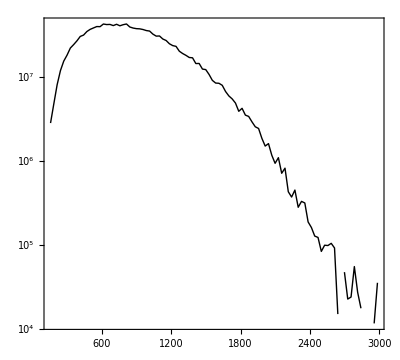

```mathematica
ListLogPlot[TrueSpectrum,Joined->True,PlotStyle->Directive[Thick,Black]]
```

#### Number of predicted full transmutation events (for normalization factor in AEDL file)

```mathematica
Total[MCEventsAll⟦All,4⟧]/Length[MCEventsAll]
Total[MCEventsNuBar⟦All,4⟧]/Length[MCEventsNuBar]
```

22382.9

17072.

#### Smearing matrix

```mathematica
SmearingMatrix=BinLists[MCEventsNuBar⟦All,{1,2,4}⟧,{BinBoundaries},{SamplingBinBoundaries},{{-∞,∞}}];
```

```mathematica
(*SmearingMatrixNormalized=Transpose[If[Total[#]==0,#,N[#/Total[#]]]&/@Transpose[SmearingMatrix]];*)
SmearingMatrixNormalized=Map[Total[#⟦All,3⟧]/Length[MCEventsNuBar]&,Flatten[SmearingMatrix,{{1},{2,3},{4}}],{2}];
OutputString="// Mapping of true neutrino energy to reconstructed energy\n"<>
"// in MiniBooNE\n"<>
"// from www-boone.fnal.gov/for_physicists/data_release/nuebar2010/\n"<>
"//\n"<>
"energy(#ERES)<\n"<>
"  @energy =\n";
For[i=1,i≤Length[SmearingMatrix],i++,
OutputString=OutputString<>"{0, "<>ToString[SamplingPoints-1]<>StringJoin[Flatten[Table[{", ",ToString[SmearingMatrixNormalized⟦i,j⟧]},{j,1,Length[SmearingMatrix⟦i⟧]}]]]<>"}";
If[i<Length[SmearingMatrix],OutputString=OutputString<>":\n"];
];
OutputString=OutputString<>";\n>\n";
Export["0-code/glb/miniboone/smearing_matrix.dat",OutputString,"Text"];
```

### Results

```mathematica
DataFiles={"2-sterile-fit/mb-nuebar.dat"};
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}]⟦All,1;;3⟧;
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->2];
logthMin[i]=Min[Data[i]⟦All,1⟧];
logthMax[i]=Max[Data[i]⟦All,1⟧];
logs22thMin[i]=N[Log10[RadToS2[10.^logthMin[i]]]];
logs22thMax[i]=N[Log10[RadToS2[10.^logthMax[i]]]];
logdmMin[i]=Min[Data[i]⟦All,2⟧];
logdmMax[i]=Max[Data[i]⟦All,2⟧];
Chi2Min[i]=Min[Data[i]⟦All,3⟧];
];
DataMB={Log10[#⟦2⟧],Log10[#⟦1⟧],#⟦3⟧}&/@Import["0-code/glb/miniboone/data/likelihoodsurface_nubar_lowe.txt","Table"];
(*DataMB={Log10[#⟦2⟧],Log10[#⟦1⟧],#⟦3⟧}&/@Import["0-code/glb/miniboone/data/effective_chi2_surface_200.txt","Table"];*)
DataMBInterpol=Interpolation[DataMB,InterpolationOrder->1];
Chi2MinMB=Min[DataMB⟦All,3⟧];
```

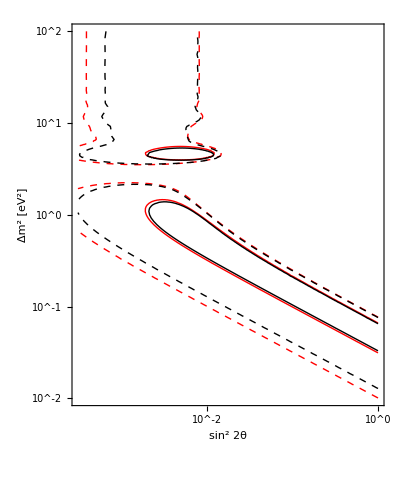

```mathematica
i=1;
MyStyles={Directive[Thick,Red,Dashing[{}]],Directive[Thick,Red,Dashed],Directive[Thick,Red,Dotted]};
MyContours={χ2[2,0.32],χ2[2,0.1],χ2[2,0.01]};
MyContours={χ2[2,0.1],χ2[2,0.01]};
Show[
ContourPlot[DataInterpol[i][Log10[S2ToRad[10.^logs22th]],logdm]-Chi2Min[i],{logs22th,-3.5,logs22thMax[i]},{logdm,logdmMin[i],logdmMax[i]},Contours->MyContours,PlotRange->Full,ContourShading->None,ContourStyle->MyStyles],
ContourPlot[DataMBInterpol[logs22th,logdm]-Chi2MinMB,{logs22th,-3.5,logs22thMax[i]},{logdm,logdmMin[i],logdmMax[i]},Contours->MyContours,ContourShading->None,ContourStyle->(Directive[#,Thickness[Medium],Black]&/@MyStyles)],
FrameLabel->{"sin^2 2θ","Δm^2 [eV^2]"},FrameTicks->{LogTicks[-4,1],LogTicks[-4,4],LogTicksNoLabel[-4,1],LogTicksNoLabel[-4,4]},AspectRatio->1.2
]
```

### MiniBooNE / SciBooNE combined analysis 2012

```mathematica
M=Import["0-code/glb/mb-2012/mb-sb-combined/total_error_matrix.bin.gz","Table"];
Eigenvalues[M]
```

{9.66216×10^6,564483.,45785.6,35474.,17609.6,13874.3,8779.72,8406.62,7961.14,5869.58,5811.2,5397.48,4569.43,4392.48,3982.26,3397.75,3181.21,2758.64,2270.93,1926.32,1767.61,1627.84,1554.81,1507.32,1307.26,1100.09,1067.06,1008.02,958.839,906.69,777.601,680.536,654.598,579.632,505.884,386.668,246.547,150.976,94.3962,60.9466,40.1562,37.1509}

```mathematica
Dir="0-code/glb/mb-2012/mb-sb-combined/";
Data[1]=Import[Dir<>"MB_mc_events.bin.gz","Table"];
Data[2]=Import[Dir<>"SB_mc_events.bin.gz","Table"];
BinBoundaries[1]=Import[Dir<>"bins.bin.gz","Table"]⟦All,1⟧;
BinBoundaries[2]=Import[Dir<>"bins.bin.gz","Table"]⟦All,2⟧;
```

```mathematica
i=1;
Data2[i]=Select[Data[i],#⟦1⟧>0&]⟦All,{3,5}⟧;
Data2[i]=BinLists[Data2[i],{BinBoundaries[i]},{{0,1*^10}}];
Data2[i]=Flatten[Data2[i]⟦All,All,All,2⟧,{{1},{2,3}}];
Data2[i]=Total/@Data2[i]
```

{{{{0.360709,0.0404912},{0.397898,0.0244523},{0.38293,0.0282324},{0.397569,0.0288966},{0.362111,0.0328622},{0.399156,0.0283877},{0.39795,0.0260157},{0.355854,0.0226681},{0.366126,0.0408656},{0.362481,0.0268509},«1119»,{0.397798,0.0283708},{0.393047,0.0314155},{0.398368,0.028803},{0.359411,0.0285048},{0.399011,0.0363726},{0.39426,0.0251887},{0.36391,0.0336241},{0.392985,0.0287577},{0.377357,0.0287309}}},«18»,{{«1»}}}

{{0.0404912,0.0244523,0.0282324,0.0288966,0.0328622,0.0283877,0.0260157,0.0226681,0.0408656,0.0268509,0.0344464,0.0366527,0.0284924,0.0282324,0.0314129,0.028687,0.0220832,0.0289031,0.036694,0.0483481,0.0285244,«1097»,0.0284503,0.0282324,0.0325605,0.062642,0.0260127,0.0287129,0.0315703,0.0304364,0.0282324,0.0254478,0.0565169,0.0283708,0.0314155,0.028803,0.0285048,0.0363726,0.0251887,0.0336241,0.0287577,0.0287309},«19»}

{37.7137,256.914,580.644,863.319,1030.25,1090.09,1089.11,1053.11,996.69,923.601,830.08,741.642,651.937,564.395,489.961,425.209,353.591,291.538,231.936,248.592}

## MINOS - 1003.0336

### Beam fluxes

```mathematica
DataFiles={
"0-code/glb/minos-nc/fluka05_le010z185i_735km_flux.txt",
"0-code/glb/minos-nc/flugg_le010z-185i_run4_735km_0kmoa_flux.txt"
};
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Import[DataFiles⟦i⟧,"Table"];
];
```

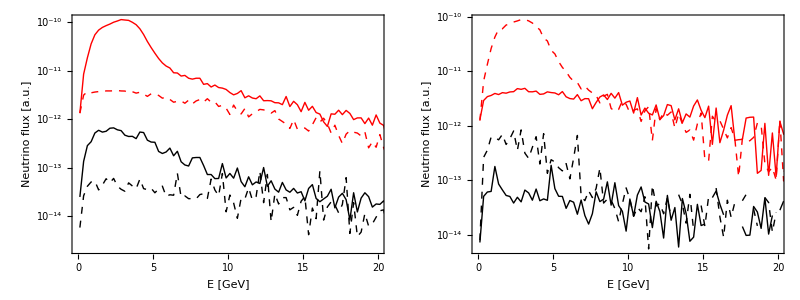

```mathematica
For[i=1,i≤Length[DataFiles],i++,
MyPlot[i]=ListLogPlot[Table[{#⟦1⟧,#⟦j⟧}&/@Data[i],{j,2,7}],Joined->True,PlotRange->{{0,20},All},
PlotStyle->{Directive[Black,Thick],Directive[Red,Thick],Directive[Blue,Thick],
Directive[Black,Dashed],Directive[Red,Dashed],Directive[Blue,Dashed]},FrameLabel->{"E [GeV]", "Neutrino flux [a.u.]"}];
];
Grid[{{MyPlot[1],MyPlot[2]}}]
```

#### Correct FD flux by using FD/ND ratio from Alex Sousa's histograms (DOESN'T REALLY LEAD TO AN IMPROVEMENT)

```mathematica
TotalFluxND=Cases[Import["0-code/glb/minos-nc/data/MINOS-total-flux-near.dat","Table"],{Repeated[_?NumericQ]}];
TotalFluxNDInterpol=Interpolation[TotalFluxND,InterpolationOrder->1];
TotalFluxFD=Cases[Import["0-code/glb/minos-nc/data/MINOS-total-flux-far.dat","Table"],{Repeated[_?NumericQ]}];
TotalFluxFDInterpol=Interpolation[TotalFluxFD,InterpolationOrder->1];
ConvertFlux[En_,x_]:=If[TotalFluxNDInterpol[En]==0,0,x*TotalFluxFDInterpol[En]/TotalFluxNDInterpol[En]];
For[i=1,i≤Length[DataFiles],i++,
DataFD[i]=Flatten[{#⟦1⟧,ConvertFlux[#⟦1⟧,#⟦2⟧],ConvertFlux[#⟦1⟧,#⟦3⟧],ConvertFlux[#⟦1⟧,#⟦4⟧],ConvertFlux[#⟦1⟧,#⟦5⟧],ConvertFlux[#⟦1⟧,#⟦6⟧],ConvertFlux[#⟦1⟧,#⟦7⟧]}]&/@Data[i];
Export[StringReplace[DataFiles⟦i⟧,".txt"->"-FD.txt"],DataFD[i],"Table"];
];
```

InterpolatingFunction::dmval: Input value {0.125`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

#### Correct fluxes by using ratio of Alex Sousa's histograms and ours (GIVES WRONG RESULTS SINCE NC SAMPLE FAVORS HIGHER ENERGIES)

```mathematica
TotalFluxND=Cases[Import["0-code/glb/minos-nc/data/MINOS-total-flux-near.dat","Table"],{Repeated[_?NumericQ]}];
TotalFluxNDInterpol=Interpolation[TotalFluxND,InterpolationOrder->1];
TotalFluxFD=Cases[Import["0-code/glb/minos-nc/data/MINOS-total-flux-far.dat","Table"],{Repeated[_?NumericQ]}];
TotalFluxFDInterpol=Interpolation[TotalFluxFD,InterpolationOrder->1];

i=1;
CorrectFlux[NormFlux_]:=Module[{Norm1,Norm2,tab},
Norm1=Total[Total[Data[i]⟦All,2;;-1⟧]];
Norm2=0.0;
tab=Table[
x=Total[Data[i]⟦j,2;;-1⟧];
Norm2+=NormFlux[Data[i]⟦j,1⟧];
{Data[i]⟦j,1⟧,If[x==0,{0,0,0,0,0,0},Data[i]⟦j,2;;-1⟧*NormFlux[Data[i]⟦j,1⟧]/x]},{j,1,Length[Data[i]]}];
Return[Flatten[{#⟦1⟧,#⟦2⟧*Norm1/Norm2}]&/@tab];
];
DataCorrectedND[i]=CorrectFlux[TotalFluxNDInterpol];
DataCorrectedFD[i]=CorrectFlux[TotalFluxFDInterpol];
Export[StringReplace[DataFiles⟦i⟧,".txt"->"-ND.txt"],DataCorrectedND[i],"Table"];
Export[StringReplace[DataFiles⟦i⟧,".txt"->"-FD.txt"],DataCorrectedFD[i],"Table"];
```

InterpolatingFunction::dmval: Input value {0.125`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.375`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.125`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.375`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

### Create dummy cross section file

```mathematica
XSTable=Table[Flatten[N[Round[{logE,ConstantArray[1./10^logE,6]},10^-5]]],{logE,-1,3,0.01}];
Export["0-code/glb/minos-nc/XFlat.dat",XSTable,"Table"];
```

### Re-interpolate smearing matrices

```mathematica
DataFiles=Union[FileNames["0-code/glb/minos-nc/data/nc_smear*"]];
Emin=0.5;
BinsReco=Flatten[{ConstantArray[0.125,60],ConstantArray[2,24],4}];
BinCentersReco=Table[Emin+Total[BinsReco⟦1;;k-1⟧]+BinsReco⟦k⟧/2,{k,1,Length[BinsReco]}];
BinsRaw=Flatten[{ConstantArray[0.125,60],ConstantArray[2,26]}];
BinCentersRaw=Table[Emin+Total[BinsRaw⟦1;;k-1⟧]+BinsRaw⟦k⟧/2,{k,1,Length[BinsRaw]}];
NData=Length[DataFiles];
Clear[S,s];
For[i=1,i≤NData,i++,
Data[i]=Import[DataFiles⟦i⟧,"Table","FieldSeparators"->{","," "},"CurrencyTokens"->{{"{","}:","};","}",",",":"},{"{","}:","};","}",",",":"}}];
Data[i]=Select[Cases[#,_Real|_Integer]&/@Data[i],Length[#]>0&];

S[i]=Array[s[i],{Length[Data[i]],Max[Data[i]⟦All,2⟧]+1}];
s[i][n_,m_]:={BinCentersReco⟦n⟧,BinCentersRaw⟦m⟧,0};
For[n=1,n≤Length[S[i]],n++,
For[m=Data[i]⟦n,1⟧+1,m≤Data[i]⟦n,2⟧+1,m++,
s[i][n,m]={BinCentersReco⟦n⟧,BinCentersRaw⟦m⟧,Data[i]⟦n,m-Data[i]⟦n,1⟧+2⟧/BinsReco⟦n⟧};
];
];
SmearInterpol[i]=Interpolation[Flatten[S[i],1],InterpolationOrder->1];
];
```

```mathematica
Integrate[SmearInterpol[1][Ereco,Eraw]/.Eraw->30,{Ereco,0,60}]
```

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint 60 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

1.00087

InterpolatingFunction::dmval: Input value {0.0010214285714285714`, 25} lies outside the range of data in the interpolating function. Extrapolation will be used.

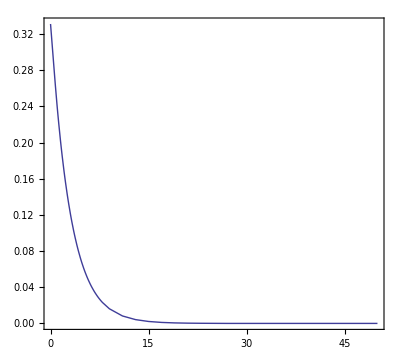

```mathematica
Plot[SmearInterpol[1][Ereco,Eraw]/.Eraw->25,{Ereco,0,50}]
```

```mathematica
MINOSEmin=0;
MINOSBinsRaw=ConstantArray[1,40];
MINOSBinsReco=ConstantArray[1,40];
MINOSBinCentersReco=Table[MINOSEmin+Total[MINOSBinsReco⟦1;;k-1⟧]+MINOSBinsReco⟦k⟧/2.,{k,1,Length[MINOSBinsReco]}];
MINOSBinCentersRaw=Table[MINOSEmin+Total[MINOSBinsRaw⟦1;;k-1⟧]+MINOSBinsRaw⟦k⟧/2.,{k,1,Length[MINOSBinsRaw]}];
MINOSSmear=Table[NIntegrate[SmearInterpol[1][Ereco,MINOSBinCentersRaw⟦m⟧],{Ereco,MINOSBinCentersReco⟦n⟧-MINOSBinsReco⟦n⟧/2.,MINOSBinCentersReco⟦n⟧+MINOSBinsReco⟦n⟧/2.}],{n,1,Length[MINOSBinsReco]},{m,1,Length[MINOSBinsRaw]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ereco near {Ereco} = {1.9791269479150333`}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ereco near {Ereco} = {2.979126947915033`}. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

```mathematica
OutStr="energy(#ERES_NC)<\n";
OutStr=OutStr<>"  @energy =\n";
For[n=1,n≤Length[MINOSBinsReco],n++,
OutStr=OutStr<>"{ 0, "<>ToString[Length[MINOSBinsRaw]-1];
For[m=1,m≤Length[MINOSBinsRaw],m++,
OutStr=OutStr<>", "<>ToString[FortranForm[MINOSSmear⟦n,m⟧]];
];
If[n<Length[MINOSBinsReco],OutStr=OutStr<>"}:\n"];
];
OutStr=OutStr<>"};\n>";
Export["0-code/glb/minos-nc/smear_NC_lbne.dat",OutStr];
```

### Convert purities to background efficiencies

FIXME : For the ND, we use the purity from Alex Sousa's MC; for the FD we could continue to use the old purity from 1001.0336 since it turns out to give better agreement with the data and MINOS MC (not sure why this is the case).

```mathematica
DataFiles="1-spectra/"<>#&/@{"minos-nc-near-noosc.dat","minos-cc-near-noosc.dat","minos-nc-far-noosc.dat","minos-cc-far-noosc.dat"};
DataFilesPur="0-code/glb/minos-nc/data/"<>#&/@{"NC-pur-near-nu2010.dat","CC-pur-near.dat","NC-pur-far-nu2010.dat","CC-pur-far.dat"};
For[i=1,i≤Length[DataFiles],i++,
DataSig[i]=glbSignalTot[Get[DataFiles⟦i⟧]];
DataBG[i]=glbBGTot[Get[DataFiles⟦i⟧]];
DataPur[i]=Cases[Import[DataFilesPur⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
DataPurInterpol[i]=Interpolation[DataPur[i],InterpolationOrder->1];

Eff[i]=Table[En=DataSig[i]⟦j,1⟧;p=DataPurInterpol[i][En];
DataSig[i]⟦j,2⟧/DataBG[i]⟦j,2⟧*(1-p)/p,{j,1,Length[DataSig[i]]}];
];
Print["ND, CC BG in NC sample:\n",Eff[1]];
Print["ND, NC BG in CC sample:\n",Eff[2]];
Print["FD, CC BG in NC sample:\n",Eff[3]];
Print["FD, NC BG in CC sample:\n",Eff[4]];
```

ND, CC BG in NC sample:
{1.12466,0.435997,0.318037,0.309596,0.328685,0.345146,0.356098,0.337814,0.300697,0.28817,0.266693,0.249046,0.245356,0.224797,0.216089,0.206548,0.197618,0.198483,0.190414,0.185443}

ND, NC BG in CC sample:
{4.04701×10^-7,7.98211×10^-7,4.52343×10^-7,3.87917×10^-7,5.80404×10^-7,9.06235×10^-7,1.2551×10^-6,1.58662×10^-6,1.72093×10^-6,1.9359×10^-6,2.3753×10^-6,2.89925×10^-6,3.4374×10^-6,4.09129×10^-6,4.8391×10^-6,5.83318×10^-6,6.14974×10^-6,7.35302×10^-6,8.47596×10^-6,0.0000101564}

FD, CC BG in NC sample:
{0.91157,0.354907,0.253365,0.25827,0.305747,0.396002,0.50077,0.558518,0.580881,0.603479,0.60703,0.630974,0.622166,0.628168,0.639896,0.624359,0.633535,0.6293,0.62291,0.621873}

FD, NC BG in CC sample:
{1.83283×10^-7,4.78383×10^-7,4.35965×10^-7,3.48988×10^-7,3.55207×10^-7,4.82656×10^-7,5.9299×10^-7,7.31885×10^-7,8.81507×10^-7,9.62447×10^-7,9.97738×10^-7,1.01635×10^-6,9.88418×10^-7,9.68773×10^-7,8.65649×10^-7,9.175×10^-7,1.04254×10^-6,1.06335×10^-6,1.19582×10^-6,1.36735×10^-6}

### Event spectra

```mathematica
DataFiles={"minos-nc-near.dat","minos-cc-near.dat","minos-nc-far.dat","minos-cc-far.dat",
{"minos-th13.dat",{1,1}},{"minos-th13.dat",{1,2}},{"minos-th13.dat",{2,1}},{"minos-th13.dat",{2,2}},
{"minos-th24.dat",{1,1}},{"minos-th24.dat",{1,2}},{"minos-th24.dat",{2,1}},{"minos-th24.dat",{2,2}},
{"minos-th34.dat",{1,1}},{"minos-th34.dat",{1,2}},{"minos-th34.dat",{2,1}},{"minos-th34.dat",{2,2}},
{"minos-bf-thomas.dat",{1,1}},{"minos-bf-thomas.dat",{1,2}},{"minos-bf-thomas.dat",{2,1}},{"minos-bf-thomas.dat",{2,2}}}/.s_String:>"1-spectra/"<>s;
DataFilesMINOS={"NC-spectrum-near-nu2010.dat","CC-spectrum-near.dat","NC-spectrum-far-nu2010.dat","CC-spectrum-far.dat"}/.s_String:>"0-code/glb/minos-nc/data/"<>s;
MyPlotLabels={"Near detector NC","Near detector CC","Far detector NC","Far detector CC"};
For[i=1,i≤Length[DataFiles],i++,
If[Head[DataFiles⟦i⟧]===List,
Data[i]=ToExpression[StringReplace[Import[DataFiles⟦i,1⟧,"Text"],RegularExpression["#.*\n"]->""]]⟦Sequence@@DataFiles⟦i,2⟧⟧,
(* Else *)
Data[i]=Get[DataFiles⟦i⟧];
];
EventsSignal[i]=glbSignalTot[Data[i]];
EventsBG[i]=glbBGTot[Data[i]];
EventsTotal[i]=glbSignalBGTot[Data[i]];
BinSizes[i]=Function[x,First[Select[{0.125,0.25,0.5,1,2,4,8},FractionalPart[1/#(x+#/2)]<1*^-10&]]]/@EventsSignal[i]⟦All,1⟧;

If[Mod[i,4]==3||Mod[i,4]==0,
EventsTotal[i]=Table[{EventsTotal[i]⟦k,1⟧,EventsTotal[i]⟦k,2⟧*DataObs[i-2]⟦k,2⟧/EventsTotal[i-2]⟦k,2⟧},{k,1,Length[EventsTotal[i]]}]
];

DataMINOS[i]=Cases[Import[DataFilesMINOS⟦Mod[i-1,4]+1⟧,"Table"],{Repeated[_?NumericQ]}];
DataObs[i]=DataMINOS[i]⟦All,{1,2}⟧;
DataMC[i]=DataMINOS[i]⟦All,{1,3}⟧;
DataBGMC[i]=DataMINOS[i]⟦All,{1,4}⟧;
];
```

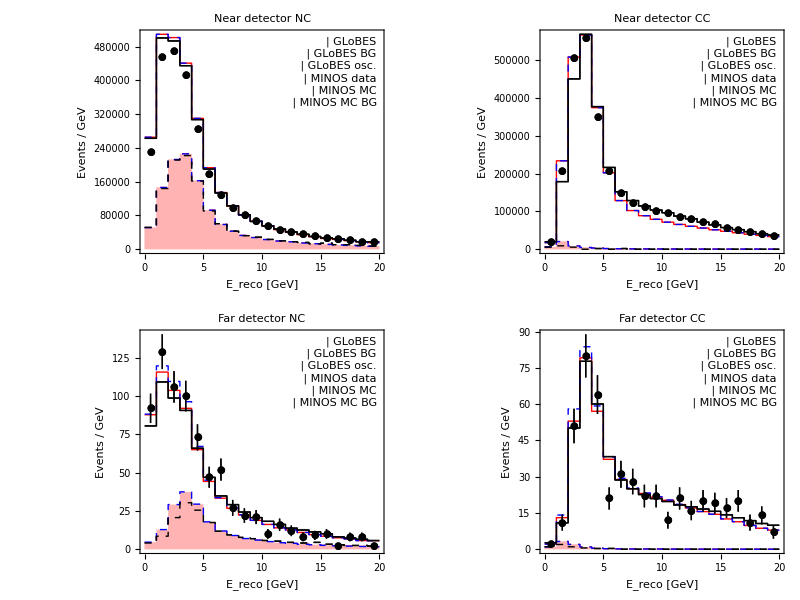

```mathematica
MyLegend=Framed[Grid[{
{LegendLine[Directive[Thick,Red]],"GLoBES"},
{LegendBox[RGBColor[1,.7,.7],Directive[Thick,Red,Dashed]],"GLoBES BG"},
{LegendLine[Directive[Thick,Blue,Dashed]],"GLoBES osc."},
{LegendDataPoint[PlotStyle->Directive[Thick,Black],PlotMarkers->{Automatic,10}],"MINOS data"},
{LegendLine[Directive[Thick,Black]],"MINOS MC"},
{LegendLine[Directive[Thick,Black,Dashed]],"MINOS MC BG"}
},Spacings->{Automatic,Automatic}, Alignment->{Left,Center}],Background->RGBColor[1,1,1,.8]];
For[i=1,i≤Length[DataFiles],i++,
PlotListObs={{#⟦1⟧,#⟦2⟧},ErrorBar[Sqrt[#⟦2⟧]]}&/@DataObs[i];
MyPlotObs[i]=ErrorListPlot[PlotListObs,PlotRange->All,PlotStyle->Directive[Thick,Black],PlotMarkers->{Automatic,10}];

PlotListMCBG=Table[x=DataBGMC[i]⟦k⟧;{x⟦1⟧-BinSizes[i]⟦k⟧/2,x⟦2⟧/BinSizes[i]⟦k⟧},{k,1,Length[BinSizes[i]]}];
AppendTo[PlotListMCBG,{PlotListMCBG⟦-1,1⟧+BinSizes[i]⟦-1⟧,PlotListMCBG⟦-1,2⟧}];
MyPlotMCBG[i]=ListPlot[PlotListMCBG,PlotStyle->Directive[Thick,Black,Dashed],Joined->True,InterpolationOrder->0];

PlotListMC=Table[x=DataMC[i]⟦k⟧;{x⟦1⟧-BinSizes[i]⟦k⟧/2,x⟦2⟧/BinSizes[i]⟦k⟧},{k,1,Length[BinSizes[i]]}];
AppendTo[PlotListMC,{PlotListMC⟦-1,1⟧+BinSizes[i]⟦-1⟧,PlotListMC⟦-1,2⟧}];
MyPlotMC[i]=ListPlot[PlotListMC,PlotStyle->Directive[Thick,Black],Joined->True,InterpolationOrder->0];

PlotListTotal[i]=Table[x=EventsTotal[i]⟦k⟧;{x⟦1⟧-BinSizes[i]⟦k⟧/2,x⟦2⟧/BinSizes[i]⟦k⟧},{k,1,Length[BinSizes[i]]}];
AppendTo[PlotListTotal[i],{PlotListTotal[i]⟦-1,1⟧+BinSizes[i]⟦-1⟧,PlotListTotal[i]⟦-1,2⟧}];
MyPlotTotal[i]=ListPlot[PlotListTotal[i],PlotStyle->Directive[Thick,If[i≤4,Red,Directive[Blue,Dashed]]],Joined->True,InterpolationOrder->0];

PlotListBG[i]=Table[x=EventsBG[i]⟦k⟧;{x⟦1⟧-BinSizes[i]⟦k⟧/2,x⟦2⟧/BinSizes[i]⟦k⟧},{k,1,Length[EventsBG[i]]}];
AppendTo[PlotListBG[i],{PlotListBG[i]⟦-1,1⟧+BinSizes[i]⟦-1⟧,PlotListBG[i]⟦-1,2⟧}];
MyPlotBG[i]=ListPlot[PlotListBG[i],PlotStyle->Directive[If[i≤4,Red,Blue],Thick,Dashed],Joined->True,InterpolationOrder->0,Filling->{{1->{0,RGBColor[1,.7,.7]}}}];

MyPlot[i]=Show[{MyPlotTotal[i],MyPlotBG[i],MyPlotMCBG[i],MyPlotMC[i],MyPlotObs[i]},FrameLabel->{"E_reco [GeV]","Events / GeV"},PlotLabel->MyPlotLabels⟦Mod[i-1,4]+1⟧,Epilog->{Inset[MyLegend,Scaled[{0.97,0.97}],{1,1}]}];
];
k=4;
Grid[{{Show[MyPlot[1],MyPlot[1+k]],Show[MyPlot[2],MyPlot[2+k]]},{Show[MyPlot[3],MyPlot[3+k]],Show[MyPlot[4],MyPlot[4+k]]}}]
If[SaveFigures,
Export["fig/spectra.eps",%];
];
```

### Fit results (verification of CC fit)

```mathematica
MINOSContoursRaw=Get["0-code/glb/minos/data/minos-contours.dat"];
BestFitNu=MINOSContoursRaw⟦1,1⟧;
Nu90=MINOSContoursRaw⟦2⟧;
Nu68=MINOSContoursRaw⟦3⟧;
BestFitNuBar=MINOSContoursRaw⟦4,1⟧;
NuBar90=MINOSContoursRaw⟦5⟧;
NuBar68=MINOSContoursRaw⟦6⟧;

i=1;
Data[i]=Cases[Import["2-smparams/th23dm31-minos.dat"],{Repeated[_Real|_Integer]}];
Data[i]={Sin[2#⟦1⟧]^2,#⟦2⟧,Min[#⟦3⟧,#⟦4⟧]}&/@Data[i];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
Chi2Min[i]=Min[Data[i]⟦All,-1⟧];
```

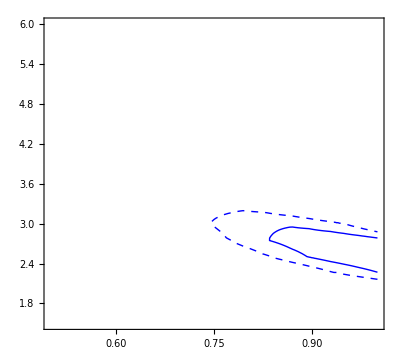

```mathematica
ContourPlot[DataInterpol[i][s22th13,dm31*1*^-3]-Chi2Min[i],{s22th13,0.5,1},{dm31,1.5,6},Contours->{χ2[2,0.32],χ2[2,0.1]},PlotRange->Full,ContourShading->False,ContourStyle->{Directive[Thick,Blue],Directive[Thick,Blue,Dashed]}]
```

### Fit results (sterile neutrino fit)

```mathematica
ParamLabels={"θ_23 [degrees]","θ_34 [degrees]","θ_24 [degrees]"};
DataFiles="3-3p1/"<>#&/@{"th23th34th24-minos-th13-0.dat","th23th34th24-minos-th13-12deg.dat"};
DataFilesMINOS=Map["0-code/glb/minos-nc/data/"<>#&,{{"fit-m4ggm3-th23-A.dat","fit-m4ggm3-th34-A.dat","fit-m4ggm3-th24-A.dat"},{"fit-m4ggm3-th23-B.dat","fit-m4ggm3-th34-B.dat","fit-m4ggm3-th24-B.dat"}},{-1}];
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Data[i]=Flatten[{#⟦1;;-3⟧,Min[#⟦-2⟧,#⟦-1⟧]}]&/@Data[i];
Chi2Min[i]=Min[Data[i]⟦All,-1⟧];
For[j=1,j≤Length[Data[1]⟦1⟧]-1,j++,
DataProj[i,j]={#⟦1,j⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦j⟧==#2⟦j⟧&];
DataProjInterpol[i,j]=Interpolation[DataProj[i,j],InterpolationOrder->1];
xmin[i,j]=Min[Data[i]⟦All,j⟧];
xmax[i,j]=Max[Data[i]⟦All,j⟧];
];
];
For[i=1,i≤Length[DataFilesMINOS],i++,
For[j=1,j≤Length[DataFilesMINOS⟦i⟧],j++,
DataMINOS[i,j]=Cases[Import[DataFilesMINOS⟦i,j⟧,"Table"],{Repeated[_?NumericQ]}];
];
];
```

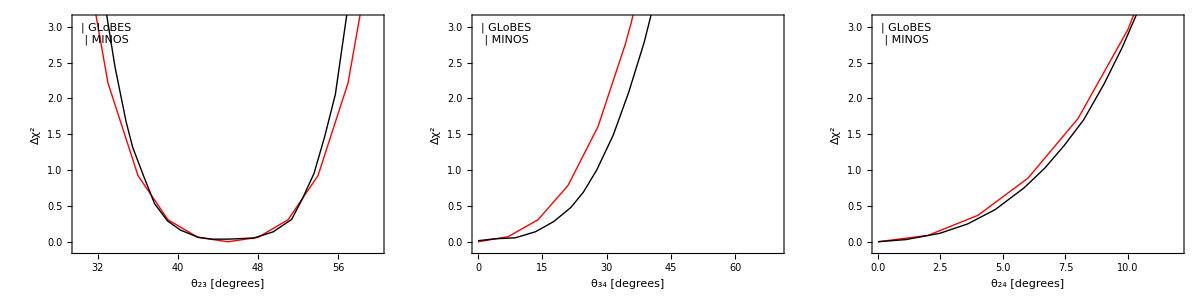

```mathematica
i=1;
MyLegend=Framed[Grid[{
{LegendLine[Directive[Thick,Red]],"GLoBES"},
{LegendLine[Directive[Thick,Black]],"MINOS"}
},Spacings->{Automatic,Automatic}, Alignment->{Left,Center}],Background->RGBColor[1,1,1,.8]];
For[j=1,j≤Length[Data[1]⟦1⟧]-1,j++,
MyPlot[i,j]=Show[
Plot[DataProjInterpol[i,j][x Degree]-Chi2Min[i],{x,xmin[i,j]/Degree,xmax[i,j]/Degree},PlotStyle->Directive[Thick,Red]],
ListPlot[DataMINOS[i,j],Joined->True,PlotStyle->Directive[Thick,Black]],
PlotRange->{-0.1,3.1},FrameLabel->{ParamLabels⟦j⟧,"Δχ^2"},Epilog->{Inset[MyLegend,Scaled[{0.03,0.97}],{-1,1}]}
]
];
Grid[{{MyPlot[i,1],MyPlot[i,2],MyPlot[i,3]}}]
If[SaveFigures,
Export["fig/fits.eps",%];
];
```

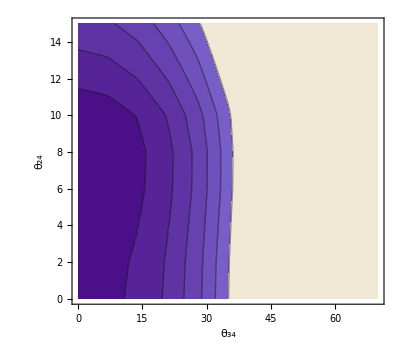

```mathematica
i=1;
DataProjTest={#⟦1,2⟧,#⟦1,3⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦{2,3}⟧==#2⟦{2,3}⟧&];
DataProjTestInterpol=Interpolation[DataProjTest,InterpolationOrder->1];
ContourPlot[DataProjTestInterpol[x Degree,y Degree]-Chi2Min[i],{x,0,70},{y,0,15},FrameLabel->{"θ_34","θ_24"},Contours->{0.5,1,1.5,2,2.5,3}]
```

## MINOS - 1003.0336 + 1103.0340

### Beam fluxes

```mathematica
DataFiles={
"0-code/glb/minos-nc/flugg_le010z185i_run1_735km_0kmoa_flux.txt",
"0-code/glb/minos-nc/flugg_le010z-185i_run4_735km_0kmoa_flux.txt"
};
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Import[DataFiles⟦i⟧,"Table"];
];
```

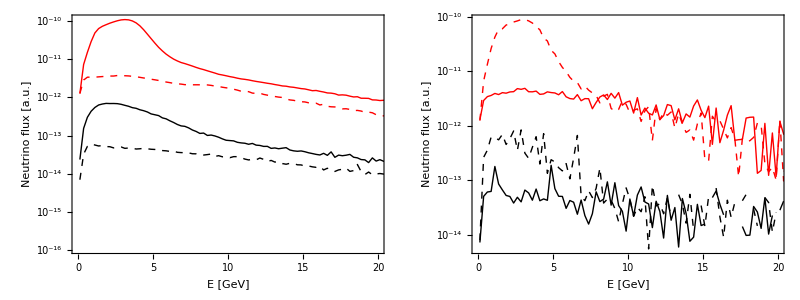

```mathematica
For[i=1,i≤Length[DataFiles],i++,
MyPlot[i]=ListLogPlot[Table[{#⟦1⟧,#⟦j⟧}&/@Data[i],{j,2,7}],Joined->True,PlotRange->{{0,20},All},
PlotStyle->{Directive[Black,Thick],Directive[Red,Thick],Directive[Blue,Thick],
Directive[Black,Dashed],Directive[Red,Dashed],Directive[Blue,Dashed]},FrameLabel->{"E [GeV]", "Neutrino flux [a.u.]"}];
];
Grid[{{MyPlot[1],MyPlot[2]}}]
```

### Preparation of input files

#### Rebinning of event spectra

NOTE : Run Event spectra code first for proper initialization

```mathematica
DataMINOS[i]=Cases[Import[DataFilesMINOS⟦Mod[i-1,4]+1⟧,"Table"],{Repeated[_?NumericQ]}];
DataObs[i]=DataMINOS[i]⟦All,{1,2}⟧;
DataMC[i]=DataMINOS[i]⟦All,{1,3}⟧;
DataBGMC[i]=DataMINOS[i]⟦All,{1,4}⟧;

(* CC ND data *)
Make1GeVBins[DataObs[2]]⟦All,2⟧

(* CC FD data *)
Make1GeVBins[DataObs[4]]⟦All,2⟧
```

{79474.4,1.08292×10^6,2.75959×10^6,2.9265×10^6,1.66333×10^6,957837.,722416.,638357.,582196.,526039.,477828.,429627.,393376.,361109.,320876.,280643.,248376.,220098.,199777.,175483.}

{8.59002,28.308,145.64,237.007,175.705,94.8805,86.2907,89.0238,92.9283,89.0239,86.6811,64.8156,68.7202,51.5401,56.2256,63.2538,46.8547,42.9501,40.6074,32.7983,163.991,109.328}

#### Compute background efficiencies

USAGE: Run event spectra code first for proper initialization. Then, run
  globes -s -c3 -m minos-cc-far.glb > minos-cc-far-NCnoeff.dat
to get rates for NC channel with *no* efficiencies. Finally, run the following code and copy the output back to the glb file.

```mathematica
i=4;
Data[i]=Get["1-spectra/minos-cc-far-NCnoeff.dat"]⟦1⟧;
(DataBGMC[i]⟦1;;Length[Data[i]]⟧/Data[i])⟦All,2⟧
```

{2.11933×10^-7,3.66763×10^-7,4.79433×10^-7,6.13481×10^-7,9.85216×10^-7,2.08878×10^-6,2.97771×10^-6,2.77602×10^-6,6.9601×10^-6,5.52704×10^-6,7.25806×10^-6,0.0000158291,0.,0.,0.,0.,0.,0.,0.,0.}

#### Efficiencies for CC events

USAGE:
- Remove efficiencies from CC channels in glb files and compute event spectra
- Run event spectra code for proper initialization.
- Then, run the code below for the *near detector* and copy the result into the glb file as @post_smearing_efficiencies
- Compute event spectra again (*without oscillations*) and run event spectra code below again. Near detector prediction should now coincide exactly with MINOS MC prediction
- Run code for *far detector* and copy the result into the glb file as @post_smearing_efficiencies

```mathematica
i=2;
Print["Near: ",(DataMC[i]⟦1;;Length[EventsTotal[i]]⟧/EventsTotal[i])⟦All,2⟧];
i=4;
n=Length[EventsTotal[i]];
Print["Far: ",(DataMC[i]⟦1;;n,2⟧-DataBGMC[i]⟦1;;n,2⟧)/(EventsTotal[i]⟦All,2⟧-DataBGMC[i]⟦1;;n,2⟧)];
```

Near: {0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,1.,1.,1.,1.,1.,1.}

Far: {0.294003,0.685595,0.698816,0.613537,0.640051,0.83512,1.00646,1.05674,1.09238,1.16574,1.16659,1.20161,1.20245,1.14027,1.13093,1.15642,1.16221,1.12668,1.10608,1.15491}

### Event spectra

```mathematica
DataFiles={"minos-nc-near","minos-cc-near","minos-nc-far","minos-cc-far",
{"minos-th24",{2,1}},{"minos-th24",{4,1}},{"minos-th24",{1,1}},{"minos-th24",{3,1}}}/.s_String:>"1-spectra/"<>s<>".dat";
DataFilesMINOS={"NC-spectrum-near-nu2010.dat","cc-1103.0340-nd.dat","NC-spectrum-far-nu2010.dat","cc-1103.0340-fd.dat"}/.s_String:>"0-code/glb/minos-nc/data/"<>s;
MyPlotLabels={"Near detector NC","Near detector CC","Far detector NC","Far detector CC"};
For[i=1,i≤Length[DataFiles],i++,
If[Head[DataFiles⟦i⟧]===List,
Data[i]=ToExpression[StringReplace[Import[DataFiles⟦i,1⟧,"Text"],RegularExpression["#.*\n"]->""]]⟦Sequence@@DataFiles⟦i,2⟧⟧,
(* Else *)
Data[i]=Get[DataFiles⟦i⟧];
];
EventsSignal[i]=glbSignalTot[Data[i]];
EventsBG[i]=glbBGTot[Data[i]];
EventsTotal[i]=glbSignalBGTot[Data[i]];

GetBinWidths[s_]:=Module[{t,j},(* This works only if the lower boundary of the 1st bin is at 0 *)
t={2*s⟦1⟧};
For[j=1,j≤Length[s]-1,j++,
AppendTo[t,2*Differences[s]⟦j⟧-t⟦j⟧];
];
Return[t];
];
BinSizes[i]=GetBinWidths[EventsSignal[i]⟦All,1⟧];

(* Load data from published MINOS plots *)
DataMINOS[i]=Cases[Import[DataFilesMINOS⟦Mod[i-1,4]+1⟧,"Table"],{Repeated[_?NumericQ]}];
DataObs[i]=DataMINOS[i]⟦All,{1,2}⟧;
DataMC[i]=DataMINOS[i]⟦All,{1,3}⟧;
DataBGMC[i]=DataMINOS[i]⟦All,{1,4}⟧;
If[Length[DataMINOS[i]⟦1⟧]>4,
DataMCosc[i]=DataMINOS[i]⟦All,{1,5}⟧;
];
];

(* Combine data into 1 GeV bins for CC ND data *)
Make1GeVBins[X_]:=Module[{j,bb,t,res},
res={};
bb=Accumulate[GetBinWidths[X⟦All,1⟧]];
t=0.0;
For[j=1,j≤Length[X],j++,
t+=X⟦j,2⟧;
If[FractionalPart[bb⟦j⟧]<1*^-10,
AppendTo[res,{bb⟦j⟧-0.5,t}];
t=0.0;
]; (* If *)
]; (* For *)
Return[res];
]; (* Module *)

Do[
DataObs[i]=Make1GeVBins[DataObs[i]];
DataMC[i]=Make1GeVBins[DataMC[i]];
DataBGMC[i]=Make1GeVBins[DataBGMC[i]];
If[Length[DataMINOS[i]⟦1⟧]>4,
DataMCosc[i]=Make1GeVBins[DataMCosc[i]];
];
(*EventsTotal[i]=Make1GeVBins[EventsTotal[i]];
EventsSignal[i]=Make1GeVBins[EventsSignal[i]];
EventsBG[i]=Make1GeVBins[EventsBG[i]];
BinSizes[i]=ConstantArray[1,Length[DataObs[i]]];*)
,{i,{2,4,6,8}}];

(* Near-far extrapolation *)
Do[
EventsTotal[i]=Table[{EventsTotal[i]⟦k,1⟧,EventsTotal[i]⟦k,2⟧*DataObs[i-2]⟦k,2⟧/EventsTotal[i-2]⟦k,2⟧},{k,1,Length[DataObs[i-2]]}];
BinSizes[i]=BinSizes[i-2];
,{i,{3,4,7,8}}];
```

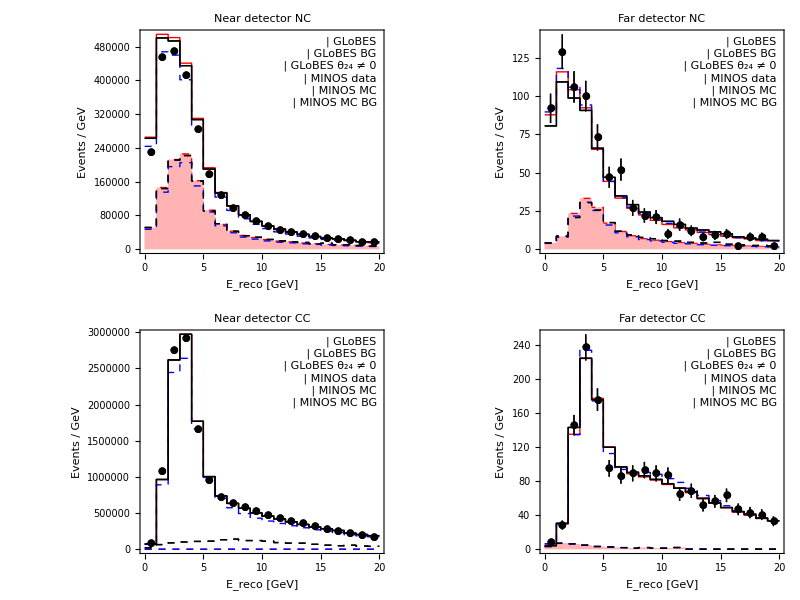

```mathematica
MyLegend=Framed[Grid[{
{LegendLine[Directive[Thick,Red]],"GLoBES"},
{LegendBox[RGBColor[1,.7,.7],Directive[Thick,Red,Dashed]],"GLoBES BG"},
{LegendLine[Directive[Thick,Blue,Dashed]],"GLoBES θ_24 ≠ 0"},
{LegendDataPoint[PlotStyle->Directive[Thick,Black],PlotMarkers->{Automatic,10}],"MINOS data"},
{LegendLine[Directive[Thick,Black]],"MINOS MC"},
{LegendLine[Directive[Thick,Black,Dashed]],"MINOS MC BG"}
},Spacings->{Automatic,Automatic}, Alignment->{Left,Center}],Background->RGBColor[1,1,1,.8]];
For[i=1,i≤Length[DataFiles],i++,
PlotListObs[i]={{#⟦1⟧,#⟦2⟧},ErrorBar[Sqrt[#⟦2⟧]]}&/@DataObs[i];
PlotListObs[i]=Table[{{DataObs[i]⟦k,1⟧,DataObs[i]⟦k,2⟧/BinSizes[i]⟦k⟧},ErrorBar[Sqrt[DataObs[i]⟦k,2⟧]/BinSizes[i]⟦k⟧]},{k,1,Length[BinSizes[i]]}];
MyPlotObs[i]=ErrorListPlot[PlotListObs[i],PlotRange->All,PlotStyle->Directive[Thick,Black],PlotMarkers->{Automatic,10}];

PlotListMCBG[i]=Table[x=DataBGMC[i]⟦k⟧;{x⟦1⟧-BinSizes[i]⟦k⟧/2,x⟦2⟧/BinSizes[i]⟦k⟧},{k,1,Length[BinSizes[i]]}];
AppendTo[PlotListMCBG[i],{PlotListMCBG[i]⟦-1,1⟧+BinSizes[i]⟦-1⟧,PlotListMCBG[i]⟦-1,2⟧}];
MyPlotMCBG[i]=ListPlot[PlotListMCBG[i],PlotStyle->Directive[Thick,Black,Dashed],Joined->True,InterpolationOrder->0];

PlotListMC[i]=Table[x=DataMC[i]⟦k⟧;{x⟦1⟧-BinSizes[i]⟦k⟧/2,x⟦2⟧/BinSizes[i]⟦k⟧},{k,1,Length[BinSizes[i]]}];
AppendTo[PlotListMC[i],{PlotListMC[i]⟦-1,1⟧+BinSizes[i]⟦-1⟧,PlotListMC[i]⟦-1,2⟧}];
MyPlotMC[i]=ListPlot[PlotListMC[i],PlotStyle->Directive[Thick,Black],Joined->True,InterpolationOrder->0];

If[Length[DataMINOS[i]⟦1⟧]>4,
PlotListMCosc[i]=Table[x=DataMCosc[i]⟦k⟧;{x⟦1⟧-BinSizes[i]⟦k⟧/2,x⟦2⟧/BinSizes[i]⟦k⟧},{k,1,Length[BinSizes[i]]}];
AppendTo[PlotListMCosc[i],{PlotListMCosc[i]⟦-1,1⟧+BinSizes[i]⟦-1⟧,PlotListMCosc[i]⟦-1,2⟧}];
MyPlotMC[i]=ListPlot[PlotListMCosc[i],PlotStyle->Directive[Thick,Black],Joined->True,InterpolationOrder->0];
];

PlotListTotal[i]=Table[x=EventsTotal[i]⟦k⟧;{x⟦1⟧-BinSizes[i]⟦k⟧/2,x⟦2⟧/BinSizes[i]⟦k⟧},{k,1,Length[BinSizes[i]]}];
AppendTo[PlotListTotal[i],{PlotListTotal[i]⟦-1,1⟧+BinSizes[i]⟦-1⟧,PlotListTotal[i]⟦-1,2⟧}];
MyPlotTotal[i]=ListPlot[PlotListTotal[i],PlotStyle->Directive[Thick,If[i≤4,Red,Directive[Blue,Dashed]]],Joined->True,InterpolationOrder->0];

PlotListBG[i]=Table[x=EventsBG[i]⟦k⟧;{x⟦1⟧-BinSizes[i]⟦k⟧/2,x⟦2⟧/BinSizes[i]⟦k⟧},{k,1,Length[BinSizes[i]]}];
AppendTo[PlotListBG[i],{PlotListBG[i]⟦-1,1⟧+BinSizes[i]⟦-1⟧,PlotListBG[i]⟦-1,2⟧}];
MyPlotBG[i]=ListPlot[PlotListBG[i],PlotStyle->Directive[If[i≤4,Red,Blue],Thick,Dashed],Joined->True,InterpolationOrder->0,Filling->{{1->{0,RGBColor[1,.7,.7]}}}];

MyPlot[i]=Show[{MyPlotTotal[i],MyPlotBG[i],MyPlotMCBG[i],MyPlotMC[i],MyPlotObs[i]},FrameLabel->{"E_reco [GeV]","Events / GeV"},PlotLabel->MyPlotLabels⟦Mod[i-1,4]+1⟧,Epilog->{Inset[MyLegend,Scaled[{0.97,0.97}],{1,1}]}];
];
k=4;
Grid[{{Show[MyPlot[1],MyPlot[1+k]],Show[MyPlot[3],MyPlot[3+k]]},{Show[MyPlot[2],MyPlot[2+k]],Show[MyPlot[4],MyPlot[4+k]]}}]
(*Grid[{{MyPlot[1],MyPlot[3]},{MyPlot[2],MyPlot[4]}}]*)
If[SaveFigures,
Export["fig/minos-spectra.eps",%];
];
```

### Fit results (verification of CC fit)

```mathematica
MINOSContoursRaw=Get["0-code/glb/minos-nc/data/cc-contours-1103.0340.dat"];
BestFitNu=MINOSContoursRaw⟦1,1⟧;
Nu90=MINOSContoursRaw⟦2⟧;
Nu68=MINOSContoursRaw⟦3⟧;

i=1;
Data[i]=Cases[Import["2-smparams/th23dm31-minos.dat"],{Repeated[_Real|_Integer]}];
Data[i]={Sin[2#⟦1⟧]^2,#⟦2⟧,Min[#⟦3⟧,#⟦4⟧]}&/@Data[i];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
Chi2Min[i]=Min[Data[i]⟦All,-1⟧];
```

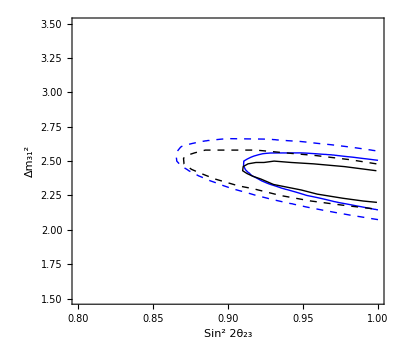

```mathematica
ContourPlot[DataInterpol[i][s22th13,dm31*1*^-3]-Chi2Min[i],{s22th13,0.8,1},{dm31,1.5,3.5},Contours->{χ2[2,0.32],χ2[2,0.1]},PlotRange->Full,ContourShading->False,ContourStyle->{Directive[Thick,Blue],Directive[Thick,Blue,Dashed]},
Epilog->{Line[{#⟦1⟧,#⟦2⟧*1000}&/@Nu68],Dashed,Line[{#⟦1⟧,#⟦2⟧*1000}&/@Nu90]},FrameLabel->{"Sin^2 2θ_23","Δm_31^2"}]
```

### Fit results (sterile neutrino fit)

```mathematica
ParamLabels={"θ_23 [degrees]","θ_34 [degrees]","θ_24 [degrees]"};
DataFiles="3-3p1/"<>#&/@{"th23th34th24-minos-th13-0.dat","th23th34th24-minos-th13-12deg.dat"};
DataFilesMINOS=Map["0-code/glb/minos-nc/data/"<>#&,{{"fit-m4ggm3-th23-A.dat","fit-m4ggm3-th34-A.dat","fit-m4ggm3-th24-A.dat"},{"fit-m4ggm3-th23-B.dat","fit-m4ggm3-th34-B.dat","fit-m4ggm3-th24-B.dat"}},{-1}];
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Data[i]=Flatten[{#⟦1;;-3⟧,Min[#⟦-2⟧,#⟦-1⟧]}]&/@Data[i];
Chi2Min[i]=Min[Data[i]⟦All,-1⟧];
For[j=1,j≤Length[Data[1]⟦1⟧]-1,j++,
DataProj[i,j]={#⟦1,j⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦j⟧==#2⟦j⟧&];
DataProjInterpol[i,j]=Interpolation[DataProj[i,j],InterpolationOrder->1];
xmin[i,j]=Min[Data[i]⟦All,j⟧];
xmax[i,j]=Max[Data[i]⟦All,j⟧];
];
];
For[i=1,i≤Length[DataFilesMINOS],i++,
For[j=1,j≤Length[DataFilesMINOS⟦i⟧],j++,
DataMINOS[i,j]=Cases[Import[DataFilesMINOS⟦i,j⟧,"Table"],{Repeated[_?NumericQ]}];
];
];
```

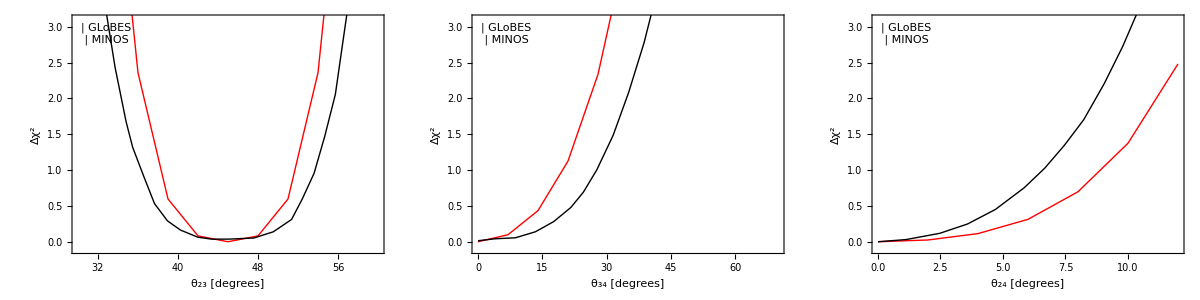

```mathematica
i=1;
MyLegend=Framed[Grid[{
{LegendLine[Directive[Thick,Red]],"GLoBES"},
{LegendLine[Directive[Thick,Black]],"MINOS"}
},Spacings->{Automatic,Automatic}, Alignment->{Left,Center}],Background->RGBColor[1,1,1,.8]];
For[j=1,j≤Length[Data[1]⟦1⟧]-1,j++,
MyPlot[i,j]=Show[
Plot[DataProjInterpol[i,j][x Degree]-Chi2Min[i],{x,xmin[i,j]/Degree,xmax[i,j]/Degree},PlotStyle->Directive[Thick,Red]],
ListPlot[DataMINOS[i,j],Joined->True,PlotStyle->Directive[Thick,Black]],
PlotRange->{-0.1,3.1},FrameLabel->{ParamLabels⟦j⟧,"Δχ^2"},Epilog->{Inset[MyLegend,Scaled[{0.03,0.97}],{-1,1}]}
]
];
Grid[{{MyPlot[i,1],MyPlot[i,2],MyPlot[i,3]}}]
If[SaveFigures,
Export["fig/fits.eps",%];
];
```

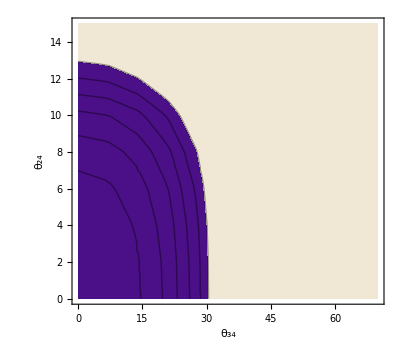

```mathematica
i=1;
DataProjTest={#⟦1,2⟧,#⟦1,3⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦{2,3}⟧==#2⟦{2,3}⟧&];
DataProjTestInterpol=Interpolation[DataProjTest,InterpolationOrder->1];
ContourPlot[DataProjTestInterpol[x Degree,y Degree]-Chi2Min[i],{x,0,70},{y,0,15},FrameLabel->{"θ_34","θ_24"},Contours->{0.5,1,1.5,2,2.5,3},PlotRange->All]
```

## Atmospheric neutrinos (courtesy of Michele Maltoni)

### Constraints on d_μ

FindMinimum::reged: The point {5.10714×10^-6} is at the edge of the search region {-5.10714×10^-6, 5.10714×10^-6} in coordinate 1 and the computed search direction points outside the region.

FindMinimum::reged: The point {0.} is at the edge of the search region {0., 0.} in coordinate 1 and the computed search direction points outside the region.

FindMinimum::reged: The point {5.10714×10^-6} is at the edge of the search region {-5.10714×10^-6, 5.10714×10^-6} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindMinimum :: reged will be suppressed during this calculation.

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

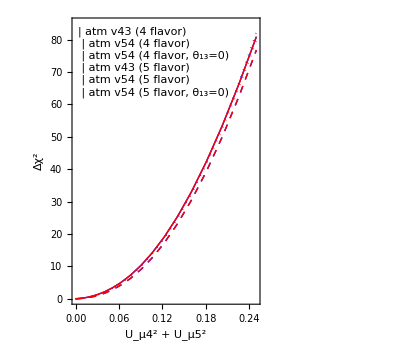

```mathematica
Data[1]=Cases[Import["0-code/old-codes/external-old/Data-files/atm-data-dmu.dat","Table"],{Repeated[_?NumericQ]}];
Data[2]={#⟦1⟧^2,#⟦2⟧^2,Min[#⟦3⟧,#⟦4⟧]}&/@Cases[Import["6-atm/Um4Um5-v43.dat.gz","Table"],{Repeated[_?NumericQ]}];
Data[3]={#⟦1⟧^2,Min[#⟦2⟧,#⟦3⟧]}&/@Cases[Import["6-atm/Um4-v43.dat.gz","Table"],{Repeated[_?NumericQ]}];
Data[4]={#⟦1⟧^2,#⟦2⟧^2,Min[#⟦3⟧,#⟦4⟧]}&/@Cases[Import["6-atm/Um4Um5-th13-0.dat.gz","Table"],{Repeated[_?NumericQ]}];
Data[5]={#⟦1⟧^2,Min[#⟦2⟧,#⟦3⟧]}&/@Cases[Import["6-atm/Um4-th13-0.dat.gz","Table"],{Repeated[_?NumericQ]}];
Data[6]={#⟦1⟧^2,#⟦2⟧^2,Min[#⟦3⟧,#⟦4⟧]}&/@Cases[Import["6-atm/Um4Um5.dat.gz","Table"],{Repeated[_?NumericQ]}];
Data[7]={#⟦1⟧^2,Min[#⟦2⟧,#⟦3⟧]}&/@Cases[Import["6-atm/Um4.dat.gz","Table"],{Repeated[_?NumericQ]}];

(* Use x=Um4^2+Um5^2, y=Um4^2-Um5^2 *)
DataInterpolFull[2]=Interpolation[Data[2],InterpolationOrder->1];
DataInterpol[2]=(FindMinimum[DataInterpolFull[j][(#+y)/2,(#-y)/2],{y,#,-#,#}]⟦1⟧&)/.{j->2};
DataInterpolFull[4]=Interpolation[Data[4],InterpolationOrder->1];
DataInterpol[4]=(FindMinimum[DataInterpolFull[j][(#+y)/2,(#-y)/2],{y,#,-#,#}]⟦1⟧&)/.{j->4};
DataInterpolFull[6]=Interpolation[Data[6],InterpolationOrder->1];
DataInterpol[6]=(FindMinimum[DataInterpolFull[j][(#+y)/2,(#-y)/2],{y,#,-#,#}]⟦1⟧&)/.{j->6};

MyLegend=Framed[Grid[{
(*{LegendLine[Black],"Thomas' table"},*)
{LegendLine[Directive[Blue,Thick,Dotted]],"atm v43 (4 flavor)"},
{LegendLine[Directive[Blue]],"atm v54 (4 flavor)"},
{LegendLine[Directive[Blue,Dashed]],"atm v54 (4 flavor, θ_13=0)"},
{LegendLine[Directive[Red, Thick, Dotted]],"atm v43 (5 flavor)"},
{LegendLine[Directive[Red]],"atm v54 (5 flavor)"},
{LegendLine[Directive[Red, Dashed]],"atm v54 (5 flavor, θ_13=0)"}
}, BaseStyle->{FontFamily->"Times",FontSize->16},Alignment->Left],Background->GrayLevel[1,0.8]];
Show[(*ListPlot[Data[1],Joined->True,PlotStyle->Black],*)
ListPlot[Transpose[{Data[3]⟦All,1⟧,Data[3]⟦All,2⟧-Data[3]⟦1,2⟧}],Joined->True,PlotStyle->Directive[Blue,Thick,Dotted]],
ListPlot[Transpose[{Data[5]⟦All,1⟧,Data[5]⟦All,2⟧-Data[5]⟦1,2⟧}],Joined->True,PlotStyle->Directive[Blue]],
ListPlot[Transpose[{Data[7]⟦All,1⟧,Data[7]⟦All,2⟧-Data[7]⟦1,2⟧}],Joined->True,PlotStyle->Directive[Blue,Dashed]],
Plot[DataInterpol[2][dmu]-DataInterpol[2][0],{dmu,0,0.25},PlotStyle->Directive[Red,Thick,Dotted]],
Plot[DataInterpol[4][dmu]-DataInterpol[4][0],{dmu,0,0.25},PlotStyle->Directive[Red]],
Plot[DataInterpol[6][dmu]-DataInterpol[6][0],{dmu,0,0.25},PlotStyle->Directive[Red,Dashed]],
PlotRange->{{0,0.25},{0,85}},
FrameLabel->{"U_μ4^2 + U_μ5^2","Δχ^2"},Epilog->{Inset[MyLegend,Scaled[{0.03,0.97}],{-1,1}]}]
```

### Constraints on SM parameters

#### θ_23 vs. θ_13 vs. Δm_31^2

```mathematica
DataFiles="6-atm/"<>#&/@{"dm31th23th13.dat.gz"};
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Data[i]={Sin[#⟦2⟧]^2,#⟦1⟧,Log10[Sin[10^#⟦3⟧]^2],Min[#⟦{-2,-1}⟧]}&/@Data[i];
Data[i,1]={#⟦1,1⟧,#⟦1,2⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦{1,2}⟧==#2⟦{1,2}⟧&]; (* dm31, th23 *)
Data[i,2]={#⟦1,1⟧,#⟦1,3⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦{1,3}⟧==#2⟦{1,3}⟧&]; (* dm31, th13 *)
Data[i,3]={#⟦1,2⟧,#⟦1,3⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦{2,3}⟧==#2⟦{2,3}⟧&]; (* th23, th13 *)

DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
DataInterpol[i,1]=Interpolation[Data[i,1],InterpolationOrder->1];
DataInterpol[i,2]=Interpolation[Data[i,2],InterpolationOrder->1];
DataInterpol[i,3]=Interpolation[Data[i,3],InterpolationOrder->1];

p1Min[i]=Min[Data[i]⟦All,1⟧];
p1Max[i]=Max[Data[i]⟦All,1⟧];
p2Min[i]=Min[Data[i]⟦All,2⟧];
p2Max[i]=Max[Data[i]⟦All,2⟧];
p3Min[i]=Min[Data[i]⟦All,3⟧];
p3Max[i]=Max[Data[i]⟦All,3⟧];

BFPoint[i]=Sort[Data[i],OrderedQ[{#1⟦-1⟧,#2⟦-1⟧}]&]⟦1⟧;
{Chi2Min[i],BFPoint[i]}=FindMinimum[DataInterpol[i][p1,p2,p3],{p1,BFPoint[i]⟦1⟧,p1Min[i],p1Max[i]},{p2,BFPoint[i]⟦2⟧,p2Min[i],p2Max[i]},{p3,BFPoint[i]⟦3⟧,p3Min[i],p3Max[i]}]/.Rule[s_,x_]:>x;
];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

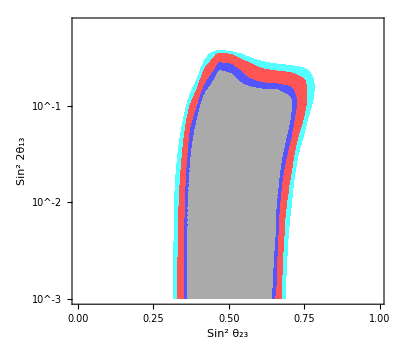
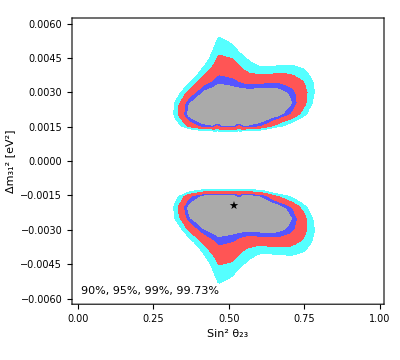
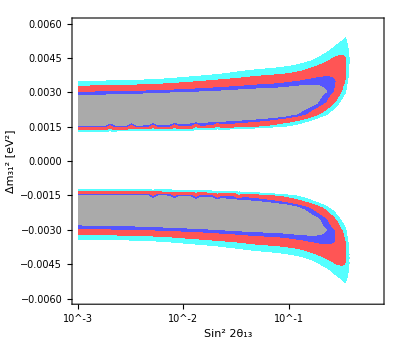
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
MyOptions={PlotRange->Full,Contours->{χ2[2,0.1],χ2[2,0.05],χ2[2,0.01],χ2[2,PValue[3]]},ContourShading->(Lighter[#]&/@{Gray,Blue,Red,Cyan,White}),ContourStyle->None,ImagePadding->{{100,10},{70,10}}};
For[i=1,i≤Length[DataFiles],i++,
MyPlot[i,1]=ContourPlot[DataInterpol[i,1][p1,p2]-Chi2Min[i],{p1,p1Min[i],p1Max[i]},{p2,p2Min[i],p2Max[i]},Evaluate[Sequence@@MyOptions],FrameLabel->{"Sin^2 θ_23","Δm_31^2 [eV^2]"},
Epilog->{
Text["★",BFPoint[i]⟦{1,2}⟧],
Text["90%, 95%, 99%, 99.73%",Scaled[{0.03,0.03}],{-1,-1}]}];
MyPlot[i,2]=ContourPlot[DataInterpol[i,2][p1,p3]-Chi2Min[i],{p1,p1Min[i],p1Max[i]},{p3,p3Min[i],p3Max[i]},Evaluate[Sequence@@MyOptions],FrameLabel->{"Sin^2 θ_23","Sin^2 2θ_13"},FrameTicks->{Automatic,LogTicks[-4,0],Automatic,LogTicksNoLabel[-4,0]}];
MyPlot[i,3]=ContourPlot[DataInterpol[i,3][p2,p3]-Chi2Min[i],{p3,p3Min[i],p3Max[i]},{p2,p2Min[i],p2Max[i]},Evaluate[Sequence@@MyOptions],FrameLabel->{"Sin^2 2θ_13","Δm_31^2 [eV^2]"},FrameTicks->{LogTicks[-4,0],Automatic,LogTicksNoLabel[-4,0],Automatic}];
];
MyGridPlot=Grid[{{MyPlot[1,2]},{MyPlot[1,1],MyPlot[1,3]}}]
If[SaveFigures,
Export["fig/atm-3flavor.pdf",MyGridPlot];
];
```

## RENO

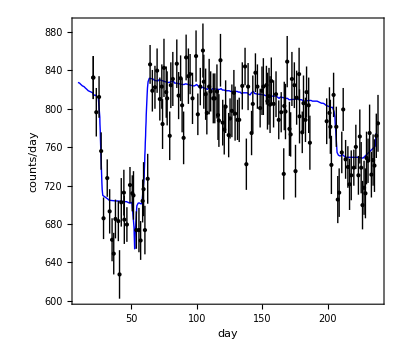

InterpolatingFunction::dmval: Input value {237.299} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {238.59} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.1863

InterpolatingFunction::dmval: Input value {237.299} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {238.59} lies outside the range of data in the interpolating function. Extrapolation will be used.

{156.594,{a→-0.0133051}}

0.190176

```mathematica
i=1;
DataObs=Cases[Import["0-code/glb/reno/nd-data.dat"],{Repeated[_?NumericQ]}];
Data[i]=Cases[Import["0-code/glb/reno/nd-prediction.dat"],{Repeated[_?NumericQ]}];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
Show[ListPlot[Data[i],Joined->True,PlotStyle->Blue],
ErrorListPlot[{{#⟦1⟧,#⟦2⟧},ErrorBar[#⟦3⟧]}&/@DataObs,PlotStyle->Black],
FrameLabel->{"day","counts/day"}]

NObsND=154088;
Chi2=Sum[(DataObs⟦j,2⟧-(1-0.012)DataInterpol[i][DataObs⟦j,1⟧])^2/DataObs⟦j,3⟧^2,{j,1,Length[DataObs]}]; (* 1.2% reduction due to theta-13 *)
1-CDF[ChiSquareDistribution[Length[DataObs]]][Chi2]

(* Fit with free normalization *)
Chi2=Sum[(DataObs⟦j,2⟧-(1+a)DataInterpol[i][DataObs⟦j,1⟧])^2/DataObs⟦j,3⟧^2,{j,1,Length[DataObs]}];
FindMinimum[Chi2,{a,0}]
1-CDF[ChiSquareDistribution[Length[DataObs]]][%⟦1⟧]
```

```mathematica
(* Alternative approach: Compute number of events in each bin from error bar, assuming it is statistical only *)
(* SEEMS *NOT* TO WORK *)
NBGND=21.75; (* events/day *)

Solve[Sqrt[(RatePaper+BGperDay)*τ]==ErrorPaper*τ,τ]
NObsND=Total[(NBGND+#⟦2⟧)*(NBGND+#⟦2⟧)/(#⟦3⟧)^2&/@DataObs]
NThND=Total[(NBGND+DataInterpol[i][#⟦1⟧])*(NBGND+#⟦2⟧)/(#⟦3⟧)^2&/@DataObs]
Chi2=(NObsND-NThND)^2/NThND
1-CDF[ChiSquareDistribution[1]][Chi2]
```

{{τ→0},{τ→(BGperDay+RatePaper)/ErrorPaper^2}}

156368.

InterpolatingFunction::dmval: Input value {237.299} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {238.59} lies outside the range of data in the interpolating function. Extrapolation will be used.

158261.

22.6481

1.94556×10^-6

```mathematica
Total[(NBGND+#⟦2⟧)/(#⟦3⟧)^2&/@DataObs]
```

195.4

## MINERνA

```mathematica
i=1;
DataFiles="9-ttt/"<>#<>".dat"&/@{"minerva-spectrum"};
Data[i]=ToExpression[StringReplace[Import[DataFiles⟦i⟧,"Text"],RegularExpression["#.*\n"]->""]];
Sig[i]=glbSignalTot[Data[1]⟦1,1⟧]
BG[i]=glbBGTot[Data[1]⟦1,1⟧]
BinWidth=Mean[Differences[Sig[i]⟦All,1⟧]];
```

{{0.5,0.506783},{1.5,12.905},{2.5,13.5132},{3.5,10.5063},{4.5,4.12897},{5.5,1.19437},{6.5,0.51899},{7.5,0.322799},{8.5,0.212653},{9.5,0.145039},{10.5,0.108304},{11.5,0.084237},{12.5,0.065951},{13.5,0.051958},{14.5,0.042563},{15.5,0.033898},{16.5,0.027777},{17.5,0.022461},{18.5,0.018939},{19.5,0.015633}}

{{0.5,0.},{1.5,0.},{2.5,0.},{3.5,0.},{4.5,0.},{5.5,0.},{6.5,0.},{7.5,0.},{8.5,0.},{9.5,0.},{10.5,0.},{11.5,0.},{12.5,0.},{13.5,0.},{14.5,0.},{15.5,0.},{16.5,0.},{17.5,0.},{18.5,0.},{19.5,0.}}

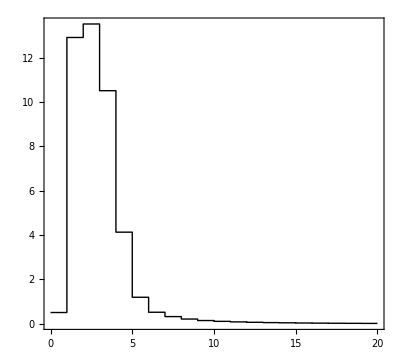

```mathematica
PlotList={#⟦1⟧-BinWidth/2,#⟦2⟧}&/@Sig[i];
AppendTo[PlotList,{PlotList⟦-1,1⟧+BinWidth,PlotList⟦-1,2⟧}];
ListPlot[PlotList,Joined->True,InterpolationOrder->0,PlotStyle->Directive[Thick,Black]]
```